# Dynamics of photoinduced PCET

## Two-state model in Redfiled approximation with no backward transitions (high-T approximation for Debye solvent)

```mathematica
Needs["BarCharts`"]
```

## Units

Unit conversion factors:

```mathematica
bohr2a=0.529177`50;
a2bohr=1/bohr2a;
au2kcal=627.5095`50;
kcal2au=1/au2kcal;
ev2cm=8065.54477`50;
cm2ev = 1/ev2cm ;
au2ev=27.2113`50;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
ev2kcal=ev2au*au2kcal;
kcal2ev=1/ev2kcal;
au2ps=2.4189`50*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
```

Physical constants:

```mathematica
hbar=1;
hbarps=0.047685388`50/(au2kcal*π);
Dalton=1822.8900409014022`50;
MassH=1.0072756064562605`50;
MassD=2.0135514936645316`50;
MassT=3.0160492`50;
mH=MassH*Dalton;
mD=MassD*Dalton;
mT=MassT*Dalton;
kb=3.16683`50*10^-6;
```

## Parameters of the two-state PCET model

Electronic coupling (kcal/mol):

```mathematica
V=0.03`50*ev2kcal
```

0.6918186562200262390991977597542197542932531705578

Bath cut-off frequency (cm^-1):

```mathematica
wc=600.0`50;
```

Bath friction constant (dimensionless):

```mathematica
η=12π;
```

Bath reorganization energy (kcal/mol) :

```mathematica
λ=hbar/π*η*wc*cm2au*au2kcal
```

20.58589744742143404949538980006340489637884198786

Kondo parameter (dimensionless):

```mathematica
α=(2η)/π
```

24

Frequencies of reactant and product proton potentials for protium (cm^-1):

```mathematica
f1=3000.0`50;
f2=3000.0`50;
```

Displacement of proton potentials (Å→ Bohr):

```mathematica
d=0.5`50*a2bohr;
```

Energy bias in two-state model (kcal/mol):

```mathematica
DG=0;
```

Temperature (K):

```mathematica
T=300;
β=1/(kb*T);
```

## Harmonic oscillator energies and wavefunction overlaps

Energy (kcal/mol):

```mathematica
HarmEnergy[n_,f_]:=Module[{omega},
omega=f*cm2au;
au2kcal*hbar*omega(n+1/2)];
```

Wavefunctions:

```mathematica
HarmWavefunction[n_,f_,x_,OptionsPattern[{M->MassH}]]:=Module[{mu,o,wnorm,w1,w2,q},
mu=OptionValue[M]*Dalton;
o=f*cm2au;
wnorm=((mu*o)/π)^(1/4)*2^(-n/2)*(n!)^(-1/2);
w1=Exp[-1/2 mu*o*x^2];
q=x*Sqrt[mu*o];
w2=HermiteH[n,q];
wnorm*w1*w2];
```

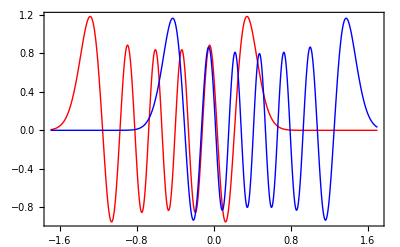

```mathematica
Plot[{HarmWavefunction[10,f1,x+d/2],HarmWavefunction[12,f1,x-d/2]},{x,-1.7,1.7},PlotRange->All,Axes->True,Frame->True,PlotStyle->{Red,Blue}]
```

Overlap integrals:

```mathematica
HarmOverlap[n1_,n2_,f1_,f2_,d_,OptionsPattern[{M->MassH,Acc->150}]]:=Module[{mass,acc,o1,o2,mu,a1,a2,s,A,Prefactor,b1,b2,i,j,Kaux},
acc=OptionValue[Acc];
mass=SetAccuracy[OptionValue[M],acc];
Kaux[i_,j_,a_,b_]:=SetAccuracy[If[OddQ[i+j],0,(i+j-1)!!/(a+b)^((i+j)/2)],acc];
mu=SetAccuracy[mass*Dalton,acc];
o1=SetAccuracy[f1*cm2au,acc];
o2=SetAccuracy[f2*cm2au,acc];
a1=SetAccuracy[(mu*o1),acc];
a2=SetAccuracy[(mu*o2),acc];
s=SetAccuracy[(a1*a2*d^2)/(a1+a2),acc];
A=SetAccuracy[(2*Sqrt[a1*a2])/(a1+a2),acc];
Prefactor=SetAccuracy[Sqrt[(A*Exp[-s])/(2^(n1+n2)*n1!*n2!)],acc];
b1=SetAccuracy[-((d*a2*Sqrt[a1])/(a1+a2)),acc];
b2=SetAccuracy[(d*a1*Sqrt[a2])/(a1+a2),acc];
Prefactor*Sum[Binomial[n1,i]*Binomial[n2,j]*HermiteH[n1-i,b1]*HermiteH[n2-j,b2]*(2*Sqrt[a1])^i*(2*Sqrt[a2])^j*Kaux[i,j,a1,a2],{j,0,n2},{i,0,n1}]];
```

```mathematica
Accuracy[HarmOverlap[10,21,f1,f2,d]]
```

130.613

## Harmonic bath quantities

```mathematica
λ kcal2au au2cm
```

7200.

Fourier transform of the e^-QS function (in high-T approximation for Debye solvent):

```mathematica
FQSH[ω_]:=Module[{omega,lambda},
omega=ω*cm2au;
lambda=λ*kcal2au;
Sqrt[(π β)/lambda]*Exp[-β(-omega+lambda)^2/(4*lambda)]
];
```

## System setup

Number of reactant and product vibronic states:

```mathematica
Nr=45;
Nk=45;
Ntot=Nr+Nk;
```

Precompute matrices of overlap integrals:

```mathematica
Clear[SH,SD];
```

```mathematica
Array[SH,{Nr,Nk},{0,0}];
Array[SD,{Nr,Nk},{0,0}];
```

```mathematica
Do[Do[SH[i,j]=HarmOverlap[i,j,f1,f2,d,M->MassH],{j,i,Nk-1}],{i,0,Nr-1}];
Do[Do[SH[j,i]=SH[i,j],{j,i+1,Nk-1}],{i,0,Nr-1}];
```

```mathematica
Do[Do[SD[i,j]=HarmOverlap[i,j,f1*Sqrt[MassH/MassD],f2*Sqrt[MassH/MassD],d,M->MassD],{j,i,Nk-1}],{i,0,Nr-1}];
Do[Do[SD[j,i]=SD[i,j],{j,i+1,Nk-1}],{i,0,Nr-1}];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

## Initial reduced density matrix

#### Pure ground vibrational state on the reactant surface

```mathematica
σ0=Table[0,{i,1,Ntot}];
σ0[[1]]=1;
```

#### Vertical excitation from the shifted electronic state

```mathematica
shift=0;
```

```mathematica
σvH=Table[
If[i≤Nr&&j≤Nr,
HarmOverlap[0,i-1,f1,f2,d+shift,M->MassH]*HarmOverlap[0,j-1,f1,f2,d+shift,M->MassH],0],{i,1,Ntot},{j,1,Ntot}];
```

```mathematica
σvD=Table[
If[i≤Nr&&j≤Nr,HarmOverlap[0,i-1,f1 √(MassH/MassD),f2 √(MassH/MassD),d+shift,M->MassD]*HarmOverlap[0,j-1,f1 √(MassH/MassD),f2 √(MassH/MassD),d+shift,M->MassD],0],{i,1,Ntot},{j,1,Ntot}];
```

```mathematica
Chop[σvH,10^-20];
```

```mathematica
Chop[σvD,10^-20];
```

```mathematica
σvdiagH=Table[σvH[[i,i]],{i,1,Ntot}];
```

```mathematica
σvdiagD=Table[σvD[[i,i]],{i,1,Ntot}];
```

```mathematica
Total[σvdiagH]
```

0.999999999999975006366698304241522396036439565318166892720588704329272452616051896195866686116205839224410032972135952650834998

```mathematica
Total[σvdiagD]
```

0.999999998366676750454485719289790287262950849659957035941061720226837431155320582605940660511349645479801451803827795798

Initial populations:

```mathematica
labellist1=ReplacePart[Table[" ",{i,1,Nr}],Table[i->i-1,{i,1,Nr,5}]];
```

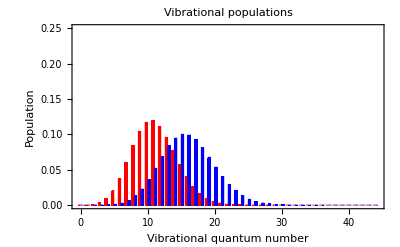

```mathematica
BarChart[{σvdiagH[[Range[1,Nr]]],σvdiagD[[Range[1,Nr]]]},BarStyle->{Red,Blue},PlotRange->{0,0.25},FrameLabel->{"Vibrational quantum number","Population"},PlotLabel->"Vibrational populations",Axes->False,Frame->True,BarLabels->labellist1]
```

Initial wavepacket (in the reactant electronic state):

```mathematica
Clear[WavevH,WavevD];
```

```mathematica
WavevH[x_]:=Sum[σvH[[i,j]]*HarmWavefunction[i-1,f1,x+d/2,M->MassH]*HarmWavefunction[j-1,f1,x+d/2,M->MassH],{i,1,Nr},{j,1,Nr}];
```

```mathematica
WavevD[x_]:=Sum[σvD[[i,j]]*HarmWavefunction[i-1,f1*Sqrt[MassH/MassD],x+d/2,M->MassD]*HarmWavefunction[j-1,f1*Sqrt[MassH/MassD],x+d/2,M->MassD],{i,1,Nr},{j,1,Nr}];
```

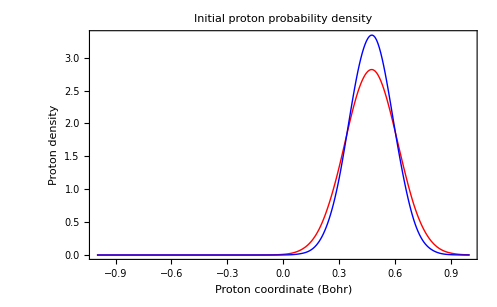

```mathematica
ListLinePlot[{Table[WavevH[x],{x,-1.0,1.0,0.1}],Table[WavevD[x],{x,-1.0,1.0,0.1}]},PlotRange->All,Axes->{False,True},Frame->True,PlotStyle->{Red,Blue},DataRange->{-1.0,1.0},InterpolationOrder->3,FrameLabel->{"Proton coordinate (Bohr)","Proton density"},PlotLabel->"Initial proton probability density"]
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

```mathematica
labellist1=ReplacePart[Table[" ",{i,1,Nr}],Table[i->i-1,{i,1,Nr,5}]];
```

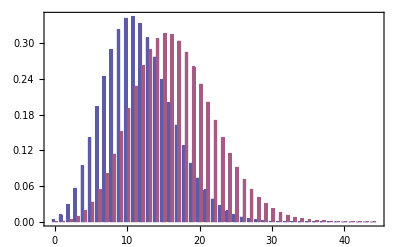

```mathematica
BarChart[{Table[SH[0,i],{i,0,Nr-1}],Table[SD[0,i],{i,0,Nr-1}]},BarLabels->labellist1,Axes->False,Frame->True]
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

## Nonadiabatic transition probabilities

Transition probability from |rμ> to |kν> (forward):

```mathematica
Clear[WforwardH,WforwardD,WbackwardH,WbackwardD]
```

```mathematica
WforwardH[nu_,mu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor,de,integral},
o1=f1;
o2=f2;
s=SH[mu,nu];
s2=s^2;
prefactor=(V*kcal2au)^2*s2;
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
de=-(enu-emu)*kcal2au*au2cm;
integral=FQSH[de];
prefactor*integral];
```

```mathematica
WforwardD[nu_,mu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor,de,integral},
o1=f1*Sqrt[MassH/MassD];
o2=f2*Sqrt[MassH/MassD];
s=SD[mu,nu];
s2=s^2;
prefactor=(V*kcal2au)^2*s2;
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
de=-(enu-emu)*kcal2au*au2cm;
integral=FQSH[de];
prefactor*integral];
```

Transition probability from |kν> to |rμ> (backward):

```mathematica
WbackwardH[mu_,nu_]:=Module[{o1,o2,s,s2,prefactor,emu,enu,de,integral},
o1=f1;
o2=f2;
s=SH[mu,nu];
s2=s^2;
prefactor=(V*kcal2au)^2*s2;
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
de=(enu-emu)*kcal2au*au2cm;
integral=FQSH[de];
prefactor*integral];
```

```mathematica
WbackwardD[mu_,nu_]:=Module[{o1,o2,s,s2,prefactor,emu,enu,de,integral},
o1=f1*Sqrt[MassH/MassD];
o2=f2*Sqrt[MassH/MassD];
s=SD[mu,nu];
s2=s^2;
prefactor=(V*kcal2au)^2*s2;
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
de=(enu-emu)*kcal2au*au2cm;
integral=FQSH[de];
prefactor*integral];
```

Distribution of transition probabilities:

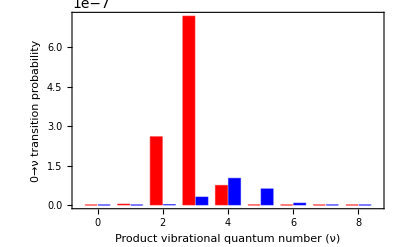

```mathematica
BarChart[{Table[WforwardH[0,i],{i,0,8}],Table[WforwardD[0,i],{i,0,8}]},Axes->False,Frame->True,FrameLabel->{"Product vibrational quantum number (ν)","0→ν transition probability"},BarStyle->{Red,Blue},BarOrientation->Vertical,BarLabels->Range[0,8]]
```

## Additional Redfield tensor components

These are complex-valued functions Γ^+ and Γ^-:

```mathematica
GammaPlusH[mu_,nu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor1,prefactor2,omega,lambda,z},
lambda=λ*kcal2au;
o1=f1;
o2=f2;
s=SH[mu,nu];
s2=s^2;
prefactor1=(V*kcal2au)^2*s2;
prefactor2=1/2 Sqrt[(π β)/lambda];
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
omega=(emu-enu)*kcal2au;
z=Abs[omega]/2 Sqrt[β/lambda];
prefactor1*prefactor2*(1+ⅈ Sign[omega]Erfi[z])*Exp[-(β omega^2)/(4*lambda)]
];
```

```mathematica
GammaMinusH[mu_,nu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor1,prefactor2,omega,lambda,z},
lambda=λ*kcal2au;
o1=f1;
o2=f2;
s=SH[mu,nu];
s2=s^2;
prefactor1=(V*kcal2au)^2*s2;
prefactor2=1/2 Sqrt[(π β)/lambda];
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
omega=(emu-enu)*kcal2au;
z=Abs[omega]/2 Sqrt[β/lambda];
prefactor1*prefactor2*(1-ⅈ Sign[omega]Erfi[z])*Exp[-(β omega^2)/(4*lambda)]
];
```

```mathematica
GammaPlusD[mu_,nu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor1,prefactor2,omega,lambda,z},
lambda=λ*kcal2au;
o1=f1*Sqrt[MassH/MassD];
o2=f2*Sqrt[MassH/MassD];
s=SD[mu,nu];
s2=s^2;
prefactor1=(V*kcal2au)^2*s2;
prefactor2=1/2 Sqrt[(π β)/lambda];
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
omega=(emu-enu)*kcal2au;
z=Abs[omega]/2 Sqrt[β/lambda];
prefactor1*prefactor2*(1+ⅈ Sign[omega]Erfi[z])*Exp[-(β omega^2)/(4*lambda)]
];
```

```mathematica
GammaMinusD[mu_,nu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor1,prefactor2,omega,lambda,z},
lambda=λ*kcal2au;
o1=f1*Sqrt[MassH/MassD];
o2=f2*Sqrt[MassH/MassD];
s=SD[mu,nu];
s2=s^2;
prefactor1=(V*kcal2au)^2*s2;
prefactor2=1/2 Sqrt[(π β)/lambda];
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
omega=(emu-enu)*kcal2au;
z=Abs[omega]/2 Sqrt[β/lambda];
prefactor1*prefactor2*(1-ⅈ Sign[omega]Erfi[z])*Exp[-(β omega^2)/(4*lambda)]
];
```

Coherence relaxation constants:

```mathematica
gammaH[mu1_,mu2_]:=Sum[GammaPlusH[mu1,nu]+GammaMinusH[mu2,nu],{nu,0,Nk-1}];
```

```mathematica
gammaD[mu1_,mu2_]:=Sum[GammaPlusD[mu1,nu]+GammaMinusD[mu2,nu],{nu,0,Nk-1}];
```

```mathematica
gammaH[1,2]
```

7.64972251992391021276023447579721992553198533051×10^-6+5.7133772638707930504841002274573939121954593×10^-6 ⅈ

```mathematica
gammaH[2,1]
```

7.64972251992391021276023447579721992553198533051×10^-6-5.7133772638707930504841002274573939121954593×10^-6 ⅈ

Precompute matrix of gamma's:

```mathematica
Array[γH,{Nr,Nr}];
Array[γD,{Nr,Nr}];
```

```mathematica
Do[γH[i,j]=gammaH[i-1,j-1],{i,1,Nr},{j,1,Nr}];
```

```mathematica
Do[γD[i,j]=gammaD[i-1,j-1],{i,1,Nr},{j,1,Nr}];
```

```mathematica
Chop[γH,10^-20];
```

```mathematica
Chop[γD,10^-20];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Piano"]],Sound[SoundNote["E",1,"Piano"]],Sound[SoundNote["G",2,"Piano"]]}]
```

## Redfield matrices (no backward transitions)

```mathematica
Clear[RRH,RRD]
```

```mathematica
RRH=
Table[
If[i≤Nr,
If[j≤Nr,If[j≠i,0,-Sum[WforwardH[k,i-1],{k,0,Nk-1}]],0],
If[j≤Nr,WforwardH[i-Nr-1,j-1],0]],{i,1,Ntot},{j,1,Ntot}];
```

```mathematica
Chop[RRH,10^-20];
```

```mathematica
RRD=
Table[
If[i≤Nr,
If[j≤Nr,If[j≠i,0,-Sum[WforwardD[k,i-1],{k,0,Nk-1}]],0],
If[j≤Nr,WforwardD[i-Nr-1,j-1],0]],{i,1,Ntot},{j,1,Ntot}];
```

```mathematica
Chop[RRD,10^-20];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Voice"]],Sound[SoundNote["E",1,"Voice"]],Sound[SoundNote["G",2,"Voice"]]}]
```

```mathematica
Accuracy[RRH]
```

52.4026

## Redfield equations and their solution

### Evolution of populations: direct diagonalization of the Redfield matrix

```mathematica
diagH=Eigensystem[RRH];
evaluesH=diagH[[1]];
MH=Transpose[diagH[[2]]];
MHr=Inverse[MH];
ΛH=DiagonalMatrix[evaluesH];
```

```mathematica
diagD=Eigensystem[RRD];
evaluesD=diagD[[1]];
MD=Transpose[diagD[[2]]];
MDr=Inverse[MD];
ΛD=DiagonalMatrix[evaluesD];
```

```mathematica
Clear[σH,σD]
```

```mathematica
σH[σ0_,t_]:=Module[{Λt,Prop},
Λt=MatrixExp[ΛH t];
Prop=MH . Λt . MHr;
Prop . σ0];
```

```mathematica
σD[σ0_,t_]:=Module[{Λt,Prop},
Λt=MatrixExp[ΛD t];
Prop=MD . Λt . MDr;
Prop . σ0];
```

### Arnoldi iteration method

```mathematica
σAH[Ndim_,σ0_,t_,OptionsPattern[{DebugOutput->False}]]:=Module[{acc,log,norm,i,j,v,u,u1,h,H,V,VT,W,Wr,Λ,diag,dim,normj},
acc=Precision[RRH];
log=OptionValue[DebugOutput];
Array[v,Ndim+1];
Array[u,Ndim+1];
Array[h,{Ndim+1,Ndim+1}];
Array[u1,Ndim+1];
Do[v[i]=0,{i,1,Ndim+1}];
Do[u[i]=0,{i,1,Ndim+1}];
Do[u1[i]=0,{i,1,Ndim+1}];
Do[h[i,j]=0,{i,1,Ndim+1},{j,1,Ndim+1}];
norm=SetPrecision[Norm[σ0],acc];
v[1]=SetPrecision[σ0/norm,acc];
u[1]=SetPrecision[σ0/norm,acc];
For[j=1,j<Ndim+1,j++,
u[j+1]=SetPrecision[RRH . v[j],acc];
For[i=1,i<j+1,i++,h[i,j]=SetPrecision[v[i].u[j+1],acc]];
u1[j+1]=u[j+1]-Sum[SetPrecision[h[k,j]*v[k],acc],{k,1,j}];
normj=SetPrecision[Norm[u1[j+1]],acc];
If[normj<10^-20,Break[],h[j+1,j]=SetPrecision[Norm[u1[j+1]],acc]];
v[j+1]=SetPrecision[u1[j+1]/h[j+1,j],acc]
];
dim=j;
H=Table[h[i,j],{i,1,dim},{j,1,dim}];
VT=Table[v[i],{i,1,dim}];
V=Transpose[VT];
diag=Eigensystem[H];
If[log,Print["Eigenvalues of h-matrix: ",diag[[1]]]];
Λ=DiagonalMatrix[diag[[1]]];
W=Transpose[diag[[2]]];
Wr=Inverse[W];
Chop[SetPrecision[V . W . MatrixExp[Λ t] . Wr . VT . σ0,acc],10^-20]
];
```

```mathematica
σAD[Ndim_,σ0_,t_,OptionsPattern[{DebugOutput->False}]]:=Module[{acc,log,norm,i,j,v,u,u1,h,H,V,VT,W,Wr,Λ,diag,dim,normj},
acc=Precision[RRD];
log=OptionValue[DebugOutput];
Array[v,Ndim+1];
Array[u,Ndim+1];
Array[h,{Ndim+1,Ndim+1}];
Array[u1,Ndim+1];
Do[v[i]=0,{i,1,Ndim+1}];
Do[u[i]=0,{i,1,Ndim+1}];
Do[u1[i]=0,{i,1,Ndim+1}];
Do[h[i,j]=0,{i,1,Ndim+1},{j,1,Ndim+1}];
norm=SetPrecision[Norm[σ0],acc];
v[1]=SetPrecision[σ0/norm,acc];
u[1]=SetPrecision[σ0/norm,acc];
For[j=1,j<Ndim+1,j++,
u[j+1]=SetPrecision[RRD . v[j],acc];
For[i=1,i<j+1,i++,h[i,j]=SetPrecision[v[i].u[j+1],acc]];
u1[j+1]=u[j+1]-Sum[SetPrecision[h[k,j]*v[k],acc],{k,1,j}];
normj=SetPrecision[Norm[u1[j+1]],acc];
If[normj<10^-20,Break[],h[j+1,j]=SetPrecision[Norm[u1[j+1]],acc]];
v[j+1]=SetPrecision[u1[j+1]/h[j+1,j],acc]
];
dim=j;
H=Table[h[i,j],{i,1,dim},{j,1,dim}];
VT=Table[v[i],{i,1,dim}];
V=Transpose[VT];
diag=Eigensystem[H];
If[log,Print["Eigenvalues of h-matrix: ",diag[[1]]]];
Λ=DiagonalMatrix[diag[[1]]];
W=Transpose[diag[[2]]];
Wr=Inverse[W];
Chop[SetPrecision[V . W . MatrixExp[Λ t] . Wr . VT . σ0,acc],10^-20]
];
```

Testing:

```mathematica
Timing@σH[σvdiagH,1ps2au][[1]]
```

{0.274123,0.000013625919738802258134308464631144719214631092}

```mathematica
Timing@σAH[15,σvdiagH,1ps2au,DebugOutput->False][[1]]
```

{0.362747,0.0000136259197388022581343084646311447185821311347}

### Evolution of coherences

```mathematica
Clear[σcH,σcD]
```

```mathematica
σcH[i_,j_,σcij0_,t_]:=Module[{o1,δω,γ},
o1=f1*cm2au;
δω=o1*(i-j);
γ=γH[i,j];
σcij0*Exp[-ⅈ*δω*t-γ*t]
];
```

```mathematica
σcD[i_,j_,σcij0_,t_]:=Module[{o1,δω,γ},
o1=f1*Sqrt[MassH/MassD]*cm2au;
δω=o1*(i-j);
γ=γD[i,j];
σcij0*Exp[-ⅈ*δω*t-γ*t]
];
```

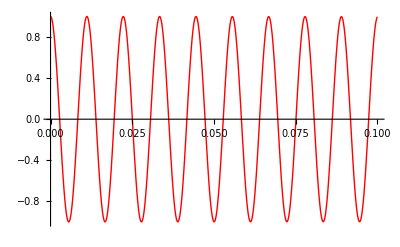

```mathematica
Plot[Re[σcH[1,2,1.0,t*ps2au]],{t,0,0.1},PlotRange->All,PlotStyle->{Red}]
```

### Dynamics of vibrational states populations

```mathematica
labellist=Flatten[{ReplacePart[Table[" ",{i,1,Nr}],Table[i->i-1,{i,1,Nr,10}]],ReplacePart[Table[" ",{i,1,Nk}],Table[i->i-1,{i,1,Nk,10}]]}];
```

```mathematica
Manipulate[BarChart[{σH[σvdiagH,t*ps2au],σD[σvdiagD,t*ps2au]},BarStyle->{Red,Blue},PlotRange->{0,0.5},FrameLabel->{"Vibrational quantum number","Population"},Axes->False,Frame->True,BarLabels->labellist],{{t,0,"Time (ps)"},0,100,0.5},FrameLabel->{None,None,"Vibrational populations"}]
```

### Dynamics of vibrational coherences

```mathematica
σvH[[1,2]]
```

0.0000456082505124067964167552569595828728580361863728902395442109252195135490441578145786819013367852580471629814022108733556675415741195115773006807822

```mathematica
Manipulate[BarChart3D[Table[If[i≠j,Re[σcH[i,j,σvH[[i,j]],t*ps2au]],0],{i,1,Nr},{j,1,Nr}],BarStyle->{LightRed},PlotRange->{-0.25,0.25},Axes->True],{{t,0,"Time (ps)"},0,5,0.1},FrameLabel->{None,None,"Imaginary parts of vibrational coherences"}]
```

## Dynamics of electronic populations

### State after vertical electronic excitation (from shifted electronic surface)

```mathematica
Total[σAH[20,σvdiagH,20ps2au]]
```

0.999999999999975006366698304241522396036439565

```mathematica
σdiagtH=Module[{i,dt,σprev,σnext,σfull,el1,el2},
σprev=σvdiagH;
σfull={};
dt=ps2au/100;
For[i=0,i<2001,i++,
σnext=σH[σprev,dt];
σfull=Append[σfull,σnext];
σprev=σnext;
];
σfull
];
```

```mathematica
σdiagtD=Module[{i,dt,σprev,σnext,σfull,el1,el2},
σprev=σvdiagD;
σfull={};
dt=ps2au/100;
For[i=0,i<2001,i++,
σnext=σD[σprev,dt];
σfull=Append[σfull,σnext];
σprev=σnext;
];
σfull
];
```

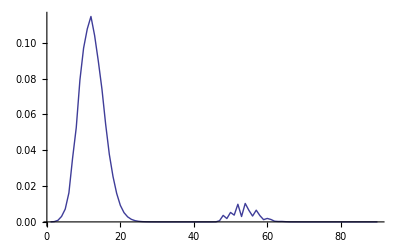

```mathematica
ListLinePlot[σdiagtH[[15,All]],PlotRange->All]
```

```mathematica
{elv1dataH,elv2dataH}=Module[{el1,el2},
el1=Sum[σdiagtH[[All,i]],{i,1,Nr}];
el2=Sum[σdiagtH[[All,i]],{i,Nr+1,Ntot}];
{el1,el2}
];
```

```mathematica
{elv1dataD,elv2dataD}=Module[{el1,el2},
el1=Sum[σdiagtD[[All,i]],{i,1,Nr}];
el2=Sum[σdiagtD[[All,i]],{i,Nr+1,Ntot}];
{el1,el2}
];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

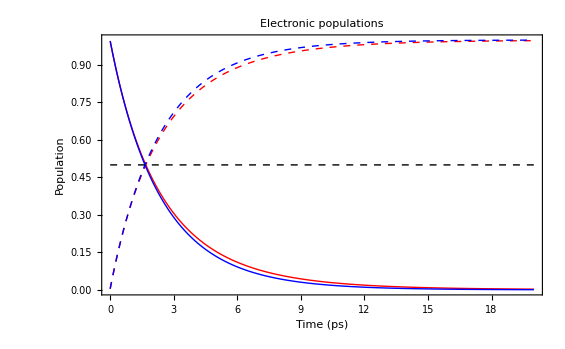

```mathematica
ListLinePlot[{elv1dataH,elv2dataH,elv1dataD,elv2dataD,Table[0.5,{t,0,20,1}]},PlotRange->{0,1},Axes->False,Frame->True,DataRange->{0,20},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed},Directive[Black,Thin,Dashed]},InterpolationOrder->2,PlotMarkers->None,FrameLabel->{"Time (ps)","Population"},PlotLabel->"Electronic populations"]
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

### Dynamics of the proton wavepackets

```mathematica
Clear[WavePacketv1H,WavePacketv2H,WavePacketv1D,WavePacketv2D]
```

```mathematica
xlist=Table[x,{x,-1.5,1.5,0.1}];
```

```mathematica
wflist1H=Table[HarmWavefunction[i-1,f1,xlist[[k]]+d/2,M->MassH],{i,1,Nr},{k,1,31}];
```

```mathematica
wflist1D=Table[HarmWavefunction[i-1,f1 √(MassH/MassD),xlist[[k]]+d/2,M->MassD],{i,1,Nr},{k,1,31}];
```

```mathematica
wflist2H=Table[HarmWavefunction[i-1,f2,xlist[[k]]-d/2,M->MassH],{i,1,Nk},{k,1,31}];
```

```mathematica
wflist2D=Table[HarmWavefunction[i-1,f2 √(MassH/MassD),xlist[[k]]-d/2,M->MassD],{i,1,Nk},{k,1,31}];
```

```mathematica
WavePacketv1H=
Table[
Sum[If[i==j,σdiagtH[[t,i]]*wflist1H[[i,k]]^2,σcH[i,j,σvH[[i,j]],(t-1)*0.01`20*ps2au]*wflist1H[[i,k]]*wflist1H[[j,k]]],{i,1,Nr},{j,1,Nr}],{t,1,2000,20},{k,1,31}];
```

```mathematica
WavePacketv2H=Table[
Sum[σdiagtH[[t,i]]*wflist2H[[i-Nr,k]]^2,{i,Nr+1,Ntot}],{t,1,2000,20},{k,1,31}];
```

```mathematica
WavePacketv1D=Table[
Sum[If[i==j,σdiagtD[[t,i]]*wflist1D[[i,k]]^2,σcD[i,j,σvD[[i,j]],(t-1)*0.01`20*ps2au]*wflist1D[[i,k]]*wflist1D[[j,k]]],{i,1,Nr},{j,1,Nr}],{t,1,2000,20},{k,1,31}];
```

```mathematica
WavePacketv2D=Table[
Sum[σdiagtD[[t,i]]*wflist2D[[i-Nr,k]]^2,{i,Nr+1,Ntot}],{t,1,2000,20},{k,1,31}];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["C",2,"Flute"]],Sound[SoundNote["B",0.5,"Flute"]],Sound[SoundNote["C",2,"Flute"]]}]
```

```mathematica
ListPlot3D[{Re[WavePacketv1H],Re[WavePacketv2H]},PlotRange->All,InterpolationOrder->3,DataRange->{{-1.5,1.5},{0,100}},AxesLabel->{"Proton coordinate (Bohr)","Time (ps)","Amplitude"},PlotLabel->"Time evolution of the vibrational wavepackets (H)",PlotStyle->{LightRed,LightBlue}]
```

-Graphics3D-

```mathematica
ListPlot3D[{Re[WavePacketv1D],Re[WavePacketv2D]},PlotRange->All,InterpolationOrder->3,DataRange->{{-1.5,1.5},{0,100}},AxesLabel->{"Proton coordinate (Bohr)","Time (ps)","Amplitude"},PlotLabel->"Time evolution of the vibrational wavepackets (D)",PlotStyle->{LightRed,LightBlue}]
```

-Graphics3D-